#### 对算符 U进行测量

```mathematica
<<Wolfram`QuantumFramework`
```

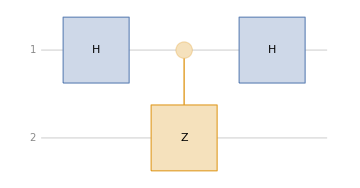

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

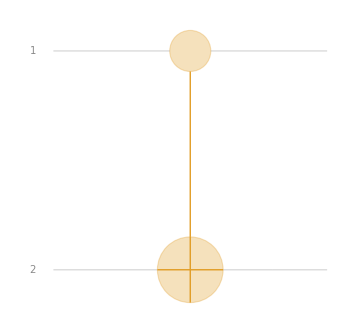

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
QuantumCircuitOperator[{"H","CZ"->{1,2},"H"}];
%//TraditionalForm
%%["Matrix"]//Normal//MatrixForm
QuantumCircuitOperator[{"CNOT"}];
%//TraditionalForm
%%["Matrix"]//Normal//MatrixForm
```

```mathematica
w= ConjugateTranspose@Reverse@(Normalize/@Eigenvectors[PauliMatrix[1]])
```

{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}}

```mathematica
Eigenvalues[PauliMatrix[3]]//N
```

{-1.,1.}

```mathematica
QuantumCircuitOperator[{"H","CX","H"}];
%["Matrix"]//Normal//MatrixForm
qc2=KroneckerProduct[IdentityMatrix[2],ConjugateTranspose@w].({{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}}).KroneckerProduct[IdentityMatrix[2],w];
qc2//MatrixForm
```

(1/2 | 1/2 | 1/2 | -1/2
1/2 | 1/2 | -1/2 | 1/2
1/2 | -1/2 | 1/2 | 1/2
-1/2 | 1/2 | 1/2 | 1/2)

(1/2 | -1/2 | 1/2 | 1/2
-1/2 | 1/2 | 1/2 | 1/2
1/2 | 1/2 | 1/2 | -1/2
1/2 | 1/2 | -1/2 | 1/2)

```mathematica
qc2.{}
```

```mathematica
#.ConjugateTranspose[#]&@({{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}})
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
cz=QuantumOperator["CZ"]["Matrix"]//Normal//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
cn=QuantumOperator["CNOT"]["Matrix"]//Normal;
sw=QuantumOperator["SWAP"]["Matrix"]//Normal;
```

```mathematica
cn//MatrixForm
sw//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
cn21=QuantumOperator["CNOT"->{2,1}]["Matrix"]//Normal;
cn21//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

```mathematica
({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}}).cn.({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}})//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

```mathematica
ih.cn.ih
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}}

```mathematica
({{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}})
```

{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}

```mathematica
KroneckerProduct[{{1,0},{0,0}},IdentityMatrix[2]]+KroneckerProduct[{{0,0},{0,1}},u]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | z | x-ⅈ y
0 | 0 | x+ⅈ y | -z)

```mathematica
$Assumptions=(x|y|z)∈Reals
```

(x|y|z)∈ℝ

```mathematica
$Assumptions=(x|y|z)∈Reals&&{x,y,z}∈Sphere[]
```

(x|y|z)∈ℝ&&{x,y,z}∈Sphere[{0,0,0}]

```mathematica
$Assumptions=.
```

```mathematica
Normalize/@Eigenvectors[u]//FullSimplify
```

{{((-1+z) √(1+z))/(√2 (x+ⅈ y)),(√(1+z))/(√2)},{(√(1+z))/(√2 Sign[x+ⅈ y]),Abs[x+ⅈ y]/(√2 √(1+z))}}

```mathematica
Eigensystem[u]
```

{{-√5,√5},{{1/2 ⅈ (-1+√5),1},{-1/2 ⅈ (1+√5),1}}}

```mathematica
u=x PauliMatrix[1]+y PauliMatrix[2]+z PauliMatrix[3]/.{x->0,y->2,z->1}
vu=Conjugate@(Normalize/@Eigensystem[u][[2]]//N)
vu.u.ConjugateTranspose[vu]//Chop//N
```

{{1,-2 ⅈ},{2 ⅈ,-1}}

{{0.-0.525731 ⅈ,0.850651},{0.+0.850651 ⅈ,0.525731}}

{{-2.23607,0.},{0.,2.23607}}

```mathematica
u=#.ConjugateTranspose[#]&@RandomReal[{},{2,2}]
vu=Normalize/@Eigensystem[u][[2]]
vu.u.ConjugateTranspose[vu]//Chop
```

{{0.709437,0.451251},{0.451251,0.81226}}

{{0.665883,0.746056},{-0.746056,0.665883}}

{{1.21502,0},{0,0.306678}}

```mathematica
$Assumptions
```

(x|y|z)∈ℝ&&{x,y,z}∈Sphere[{0,0,0}]

```mathematica
vu=((Normalize/@Eigensystem[u][[2]])//FullSimplify)/.Sign[x+ⅈ y]->(x+I y)/Abs[x+ⅈ y]/.Abs[x+ⅈ y]->√(x^2+y^2)//FullSimplify//Conjugate//Reverse
```

{{Root0.851 ⅈRoot[1+5 #1^2+5 #1^4&,4]0.,√(2/(5+√5))},{Root-0.526 ⅈRoot[1+5 #1^2+5 #1^4&,1]0.,√(1/10 (5+√5))}}

```mathematica
simConj[x_]:=(x//.{Abs[m_]^2:>Conjugate[m]m,Conjugate[m_+y_]:>Conjugate[m]+Conjugate[y],Conjugate[m_ y_]:>Conjugate[m] Conjugate[y]})/.Conjugate[k_]:>Simplify[Conjugate[k]]
```

```mathematica
vu[[1]].ConjugateTranspose[vu[[2]]]//FullSimplify
```

0

```mathematica
u.vu[[1]]//FullSimplify
```

{((x-ⅈ y)^2 √(1-z)+z √((x^2+y^2) (1+z)))/(√2 (x-ⅈ y)),(1+2 ⅈ x y-2 y^2-z)/(√(2-2 z))}

```mathematica
u=x PauliMatrix[1]+y PauliMatrix[2]+z PauliMatrix[3]
```

{{z,x-ⅈ y},{x+ⅈ y,-z}}

```mathematica
/.{x->1,y->0,z->0}
```

```mathematica
u=x PauliMatrix[1]+y PauliMatrix[2]+z PauliMatrix[3];
vu=((Normalize/@Eigensystem[u][[2]])//FullSimplify)/.Sign[x+ⅈ y]->(x+I y)/Abs[x+ⅈ y]/.Abs[x+ⅈ y]->√(x^2+y^2)//FullSimplify//Conjugate//Reverse//Simplify
vu.u.ConjugateTranspose[vu]/.x^2+y^2->1-z^2//FullSimplify//Chop
```

{{(√((x^2+y^2) (1+z)))/(√2 (x-ⅈ y)),(√(1-z))/(√2)},{((-1+z) √(1+z))/(√2 (x-ⅈ y)),(√(1+z))/(√2)}}

{{1,0},{0,-1}}

```mathematica
u.(Conjugate@vu)[[1]]-(Conjugate@vu)[[1]]//Chop
```

{0,0}

```mathematica
Clear[x,y,z]
```

```mathematica
x=√(3./6);y=√(1/6);z=√(2/6);
```

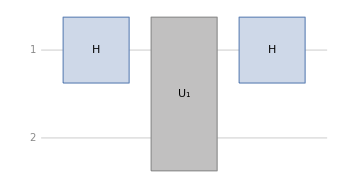

```mathematica
c1=QuantumCircuitOperator[{"H",QuantumOperator[KroneckerProduct[{{1,0},{0,0}},IdentityMatrix[2]]+KroneckerProduct[{{0,0},{0,1}},u]]->{1,2},"H"}];
c1//TraditionalForm
```

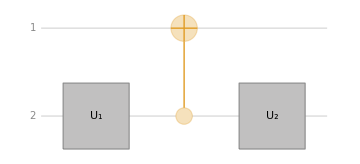

```mathematica
c2=QuantumCircuitOperator[{QuantumOperator[vu]->2,"CNOT"->{2,1},QuantumOperator[ConjugateTranspose[vu]]->2}];
c2//TraditionalForm
```

```mathematica
m1=c1["Matrix"]//Normal//FullSimplify
m2=c2["Matrix"]//Normal//FullSimplify
%-%%//FullSimplify//Chop
```

{{(1+z)/2,1/2 (x-ⅈ y),(1-z)/2,1/2 (-x+ⅈ y)},{1/2 (x+ⅈ y),(1-z)/2,1/2 (-x-ⅈ y),(1+z)/2},{(1-z)/2,1/2 (-x+ⅈ y),(1+z)/2,1/2 (x-ⅈ y)},{1/2 (-x-ⅈ y),(1+z)/2,1/2 (x+ⅈ y),(1-z)/2}}

{{(1+z)/2,(1-z^2)/(2 x+2 ⅈ y),(1-z)/2,(-1+z^2)/(2 (x+ⅈ y))},{(1-z^2)/(2 x-2 ⅈ y),(1-z)/2,(-1+z^2)/(2 (x-ⅈ y)),(1+z)/2},{(1-z)/2,(-1+z^2)/(2 (x+ⅈ y)),(1+z)/2,(1-z^2)/(2 x+2 ⅈ y)},{(-1+z^2)/(2 (x-ⅈ y)),(1+z)/2,(1-z^2)/(2 x-2 ⅈ y),(1-z)/2}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
m1.ConjugateTranspose[m1]//FullSimplify
m2.ConjugateTranspose[m2]//FullSimplify
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
m2.{(√((x^2+y^2) (1+z)))/(√2 (x-ⅈ y)),(√(1-z))/(√2),0,0}-{(√((x^2+y^2) (1+z)))/(√2 (x-ⅈ y)),(√(1-z))/(√2),0,0}//FullSimplify
```

{((-1+z) ((x-ⅈ y) √(1+z)+√((x^2+y^2) (1+z))))/(2 √2 (x-ⅈ y)),((1+z) (-((x-ⅈ y) √(1-z))+(-1+z) √(1+z)))/(2 √2 (x-ⅈ y)),-((-1+z) ((x-ⅈ y) √(1+z)+√((x^2+y^2) (1+z))))/(2 √2 (x-ⅈ y)),((1+z) ((x-ⅈ y) √(1-z)-(-1+z) √(1+z)))/(2 √2 (x-ⅈ y))}

```mathematica
m2.{Sequence@@(Conjugate@vu)[[1]],0,0}//FullSimplify
```

{-((1+z) (-√(1-z)+√(1-z) z-√((x^2+y^2) (1+z))))/(2 √2 (x+ⅈ y)),(√(1-z)-√(1-z) z+√((x^2+y^2) (1+z)))/(2 √2),((-1+z) (√(1-z)+√(1-z) z-√((x^2+y^2) (1+z))))/(2 √2 (x+ⅈ y)),(√(1-z)+√(1-z) z-√((x^2+y^2) (1+z)))/(2 √2)}

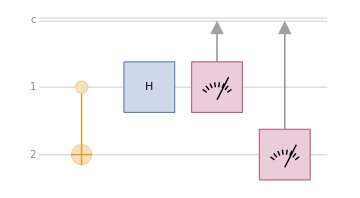

```mathematica
qco1=QuantumCircuitOperator[{"CNOT","H"->1,{1},{2}}];
qco1["Diagram"]
qco1["Matrix"]//Normal//MatrixForm;
```

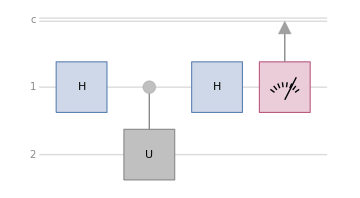

```mathematica
QuantumCircuitOperator[{"H",QuantumOperator[KroneckerProduct[{{1,0},{0,0}},IdentityMatrix[2]]+KroneckerProduct[{{0,0},{0,1}},u]]->{1,2},"H"}];
c1=QuantumCircuitOperator[{"H",QuantumOperator[{"Controlled",U},{1,2}],"H",{1}}]//TraditionalForm
```

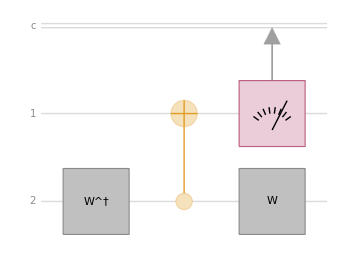

```mathematica
QuantumCircuitOperator[{QuantumOperator[vu,"Label"->"W^†"]->2,"CNOT"->{2,1},QuantumOperator[ConjugateTranspose[vu],"Label"->"W"]->2,{1}}];
%//TraditionalForm
```

```mathematica
NIntegrate
```

```mathematica
NIntegrate[τ+t,{t,τ}∈Triangle[]]
```

0.333333

```mathematica
Polygon
```

```mathematica
Triangle
```

```mathematica
sol/.α->(t.h.t.h//FullSimplify)[[1,1]]/.β->(t.h.t.h//FullSimplify)[[1,2]]//FullSimplify//N
2ArcCos[Cos[π/8]^2]//N
```

{{x→0.678598,y→-0.281085,z→-0.678598,θ→1.09606},{x→-0.678598,y→0.281085,z→0.678598,θ→-1.09606}}

1.09606

```mathematica
{x,y,z}/.{x->0.6785983445458471,y->-0.28108463771482023,z->-0.6785983445458471,θ->1.0960568152406236}//Norm
```

1.

```mathematica
{Cos[π/8],Sin[π/8],Cos[π/8]}//Norm//N
```

1.36145

```mathematica
Cos[π/8]//ToRadicals
```

(√(2+√2))/2

```mathematica
Mod
```

```mathematica
QuantumBasis[2,2,2]["ElementAssociation"]
```

<|0000→{{{{1,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}},0001→{{{{0,1},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}},0010→{{{{0,0},{1,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}},0011→{{{{0,0},{0,1}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}},0100→{{{{0,0},{0,0}},{{1,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}},0101→{{{{0,0},{0,0}},{{0,1},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}},0110→{{{{0,0},{0,0}},{{0,0},{1,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}},0111→{{{{0,0},{0,0}},{{0,0},{0,1}}},{{{0,0},{0,0}},{{0,0},{0,0}}}},1000→{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{1,0},{0,0}},{{0,0},{0,0}}}},1001→{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,1},{0,0}},{{0,0},{0,0}}}},1010→{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{1,0}},{{0,0},{0,0}}}},1011→{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,1}},{{0,0},{0,0}}}},1100→{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{1,0},{0,0}}}},1101→{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,1},{0,0}}}},1110→{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{1,0}}}},1111→{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,1}}}}|>

```mathematica
QuantumTensorProduct[,QuantumState["0"]]
```

Failure[…]

```mathematica
basis=QuantumBasis[{2,2,2}]
```

QuantumBasis[…]

```mathematica
basis["Elements"]
```

{{{{1,0},{0,0}},{{0,0},{0,0}}},{{{0,1},{0,0}},{{0,0},{0,0}}},{{{0,0},{1,0}},{{0,0},{0,0}}},{{{0,0},{0,1}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{1,0},{0,0}}},{{{0,0},{0,0}},{{0,1},{0,0}}},{{{0,0},{0,0}},{{0,0},{1,0}}},{{{0,0},{0,0}},{{0,0},{0,1}}}}

```mathematica
Array
```

```mathematica
QuantumState[{1,0}]
```

QuantumState[…]